```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
r=0.2;
cr={0.45,0.55};
NN=13;
Δθ=2π/NN;
Δl=2 r Sin[Δθ/2];
```

```mathematica
(*table of positions of the polygon vertices on the 2d mesh*)
```

```mathematica
tabr=Table[cr +r{Cos[n Δθ],Sin[n Δθ]},{n,0,NN}];
```

```mathematica
(*table of the poisitions of the line-mesh vertices, corresponding to the polygon vertices in tabr*)
```

```mathematica
tabs=Table[Δl n,{n,0,NN}]
```

{0.,0.0957263,0.191453,0.287179,0.382905,0.478631,0.574358,0.670084,0.76581,0.861536,0.957263,1.05299,1.14872,1.24444}

```mathematica
(*1 check transfer for scalar*)
```

```mathematica
(*1.1 transfer from 2d mesh to line mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
u2d[x_]:=1+x[[1]]^2 + 2 x[[2]]^2
```

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[u2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])],{s,(i-1)Δl,i Δl}]];
]
```

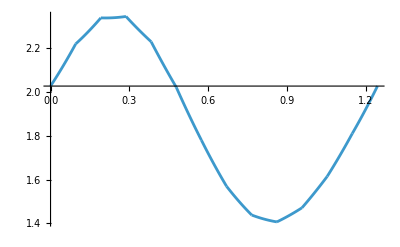

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,1]]},{i,2,Length[tline]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

{{All,2}}

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}];
```

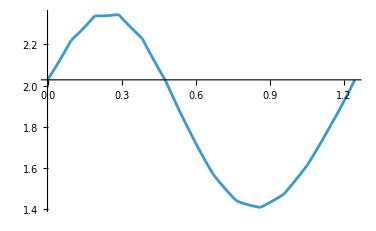

```mathematica
Show[plot2d,plottline]
```

```mathematica
(*1.2 transfer from line mesh to 2d mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
uline[x_]:=Cos[2 π x/L1]
```

```mathematica
plotline={};
For[i=1,i<=NN,i++,
AppendTo[plotline,
ParametricPlot3D[
Flatten[{tabr[[i]]+(s-(i-1)Δl)/Δl*(tabr[[i+1]]-tabr[[i]]),uline[tabs[[i]]+(s-(i-1)Δl)/Δl *(tabs[[i+1]]-tabs[[i]])]}],
{s,(i-1)Δl,i Δl}]
];

]
```

```mathematica
plotline=Show[plotline,PlotRange->Full]
```

-Graphics3D-

```mathematica
t2d=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_2d.csv"][[2;;]];
t2d=Table[{t2d[[i,2]],t2d[[i,3]],t2d[[i,1]]},{i,2,Length[t2d]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_2d.csv not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

Part::partw: Part 3 of 2;;All does not exist.

{{All,$Failed⟦2;;All⟧⟦2,3⟧,2}}

```mathematica
plot2d=ListPointPlot3D[t2d,PlotStyle->{Red,PointSize->0.02}]
```

-Graphics3D-

```mathematica
Show[plotline,plot2d,AspectRatio->1]
```

-Graphics3D-

```mathematica
(*2 check transfer for vector*)
```

```mathematica
(*2.1 transfer from 2d mesh to line mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
v2d[x_]:={1-x[[1]] + 2 x[[2]]^2,1-4x[[1]]^2 + 2 x[[2]]^2}
```

```mathematica
component=2;
```

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[v2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])][[component]],{s,(i-1)Δl,i Δl}]];
]
```

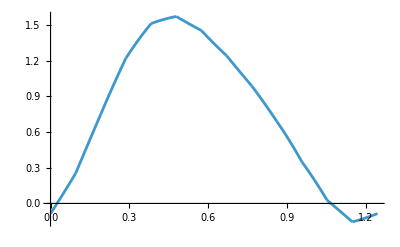

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_line.csv"][[2;;]];
tline=Table[{tline[[i,4]],tline[[i,component]]},{i,2,Length[tline]}]
```

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}];
```

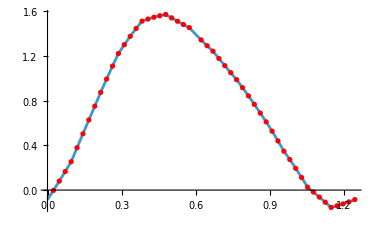

```mathematica
Show[plot2d,plottline]
```

```mathematica
(*2.2 transfer from line mesh to 2d mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
vline[x_]:={Cos[2 π x/L1],Sin[4 π x/L1]}
```

```mathematica
component=2;
```

```mathematica
plotline={};
For[i=1,i<=NN,i++,
AppendTo[plotline,
ParametricPlot3D[
Flatten[{tabr[[i]]+(s-(i-1)Δl)/Δl*(tabr[[i+1]]-tabr[[i]]),vline[tabs[[i]]+(s-(i-1)Δl)/Δl *(tabs[[i+1]]-tabs[[i]])][[component]]}],
{s,(i-1)Δl,i Δl}]
];

]
```

```mathematica
plotline=Show[plotline,PlotRange->Full]
```

-Graphics3D-

```mathematica
t2d=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_2d.csv"][[2;;]];
t2d=Table[{t2d[[i,4]],t2d[[i,5]],t2d[[i,component]]},{i,2,Length[t2d]}]
```

```mathematica
plot2d=ListPointPlot3D[t2d,PlotStyle->{Red,PointSize->0.02}]
```

-Graphics3D-

```mathematica
Show[plotline,plot2d,AspectRatio->1]
```

-Graphics3D-

```mathematica
(*3 check transfer for tensor*)
```

```mathematica
(*3.1 transfer from 2d mesh to line mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
t2d[x_]:={{Cos[2π (x[[1]]*x[[2]])],Sin[2 π x[[1]]]-Sin[2 π x[[2]]],(Sin[2 π x[[1]]]-Sin[2 π x[[2]]])^2},{Cos[2 π x[[1]]]^2-Sin[2 π x[[2]]],Cos[2π x[[1]]]^3-Sin[2 π (x[[1]]+x[[2]])],(Cos[2π x[[1]]]^3-Sin[2 π (x[[1]]+x[[2]])])^2}}
```

```mathematica
component1=2;
component2=3;
```

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[t2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])][[component1,component2]],{s,(i-1)Δl,i Δl}]];
]
```

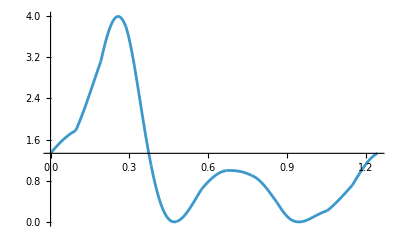

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/t_line.csv"][[2;;]];
tline=Table[{tline[[i,7]],tline[[i,1+3*(component1-1)+(component2-1)]]},{i,2,Length[tline]}]
```

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}];
```

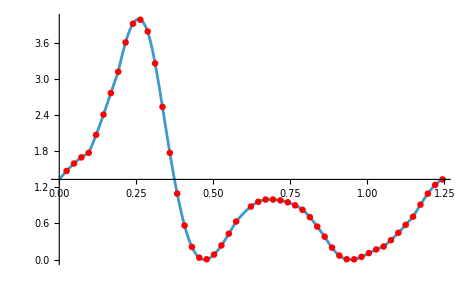

```mathematica
Show[plot2d,plottline]
```

```mathematica
(*3.2 transfer from line mesh to 2d mesh *)
```

```mathematica
(*test case 1*)
```

```mathematica
Clear[tline]
```

```mathematica
tline[x_]:={{Cos[2 π x/L1],Sin[4 π x/L1],Sin[2π x/L1]^2},{Sin[4π x/L1]^2,Sin[6π x/L1],Sin[6π x/L1]^2}}
```

```mathematica
component1=2;
component2=3;
```

```mathematica
plotline={};
For[i=1,i<=NN,i++,
AppendTo[plotline,
ParametricPlot3D[
Flatten[{tabr[[i]]+(s-(i-1)Δl)/Δl*(tabr[[i+1]]-tabr[[i]]),tline[tabs[[i]]+(s-(i-1)Δl)/Δl *(tabs[[i+1]]-tabs[[i]])][[component1,component2]]}],
{s,(i-1)Δl,i Δl}]
];

]
```

```mathematica
plotline=Show[plotline,PlotRange->Full]
```

-Graphics3D-

```mathematica
t2d=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/t_2d.csv"][[2;;]];
t2d=Table[{t2d[[i,7]],t2d[[i,8]],t2d[[i,1+3*(component1-1)+(component2-1)]]},{i,2,Length[t2d]}]
```

```mathematica
plot2d=ListPointPlot3D[t2d,PlotStyle->{Red,PointSize->0.02}]
```

-Graphics3D-

```mathematica
Show[plotline,plot2d,AspectRatio->1]
```

-Graphics3D-